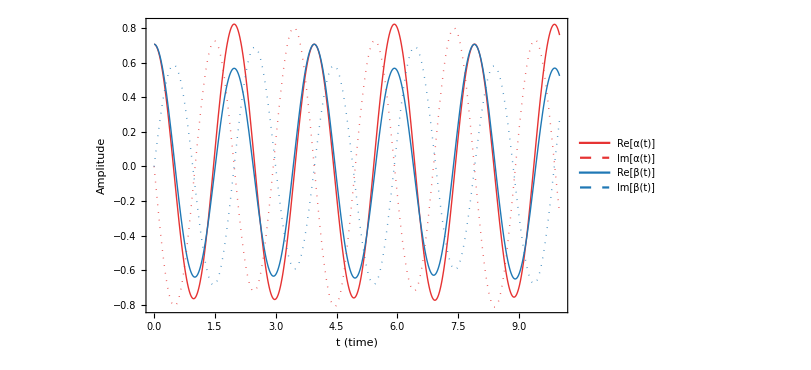

```mathematica
ClearAll["Global`*"];

(*constants*)
h=6.62607015*10^-34;
w0=2 Pi;
wm=Pi/2;

(*angle schedule*)
theta0=Pi/3;
theta[t_]:=theta0;

(*Hamiltonian pieces*)
phi[t_]:=Mod[wm t,2 Pi];
Ω[t_]:=Sin[theta[t]];
Δ[t_]:=Cos[theta[t]];

H[t_]:=(h/2) {{w0,Ω[t] Exp[-I phi[t]]},{Ω[t] Exp[+I phi[t]],-w0}};

(*Schrödinger equation*)
sol=First@NDSolve[{I h D[{alpha[t],beta[t]},t]==H[t].{alpha[t],beta[t]},alpha[0]==1/Sqrt[2],beta[0]==1/Sqrt[2]},{alpha,beta},{t,0,10}];

colA=RGBColor[0.90,0.20,0.20];  (*α curves:red*)
colB=RGBColor[0.12,0.47,0.71];  (*β curves:blue*)

(*For ReImPlot:one pair {Re,Im} per function*)
plotStyles={{Directive[colA,Thick],Directive[colA,Dashed]},(*α:Re solid,Im dashed*){Directive[colB,Thick],Directive[colB,Dashed]}   (*β:Re solid,Im dashed*)};

legendStyles=Flatten[plotStyles];  (*4 entries for the legend*)
labels={"Re[α(t)]","Im[α(t)]","Re[β(t)]","Im[β(t)]"};

(*-----plot-----*)
plt=ReImPlot[Evaluate@({alpha[t],beta[t]}/. sol),{t,0,10},PlotStyle->plotStyles,(*<<key fix:nested style pairs*)PlotRange->All,Frame->True,FrameLabel->(Style[#,14]&/@{"t (time)","Amplitude"}),PlotTheme->None,(*avoid theme overriding styles*)ImageSize->600,PlotLegends->Placed[LineLegend[legendStyles,labels,LegendLayout->"Column",LabelStyle->12,LegendMarkerSize->20,LegendFunction->(Framed[#,Background->White,FrameMargins->Small,RoundingRadius->3]&)],Right]];

plt

(* ===Export as PDF===*)
(*
dir=Quiet@Check[NotebookDirectory[],Directory[]];
file=FileNameJoin[{dir,"wavefunction_ReImPlot.pdf"}];
Export[file,plt,"PDF"];
Print["Saved PDF → ",file];
*)
```